## Studying symbols on arxiv.org

### Names of arXiv’s

```mathematica
SetDirectory[NotebookDirectory[]<>"Data\\9912"];
arXivNamesList=FileNames[];
arXivColorList=Table[RGBColor[0.05 i,1-0.05 i,0.05 i],{i,Length[arXivNamesList]}];
colorAssoc=AssociationThread[arXivNamesList,arXivColorList];
```

### Extracting the Data Paths and File Names

```mathematica
currentDirectory =SetDirectory[NotebookDirectory[]];
dataPath = currentDirectory<>"\\Data";
yearMonthConvertor[yearmonthObject_]:=DateString[yearmonthObject,#]&/@{"YearShort","Month"};
allFileNames[yearmonthObject_,arXivType_]:=FileNames["*",dataPath<>"\\"<>(StringJoin@yearMonthConvertor[yearmonthObject])<>"\\"<>arXivType<>"\\*"];
```

### Special Characters

```mathematica
listofspecialchars=Alphabet["Greek"];
```

### Number of special characters

```mathematica
howmany[article_,specialCharacter_]:= Module[{cleandatacases,spclchar},cleandatacases=StringCases[StringDelete[StringReplace[Import[article,"Text"],"%"->"1"],"m:"],Shortest["<math"~~___~~"</math>"]];
spclchar=DeleteCases[StringCases[#, Shortest["<math"~~___~~specialCharacter~~___~~"</math>"]]&/@cleandatacases,{}]//Flatten
]//Length;
howMany[yearmonthObject_,arXivType_,specialCharacter_]:=Flatten[{yearmonthObject,{Length[#],Total[#]}&[ParallelMap[howmany[#,specialCharacter]&,allFileNames[yearmonthObject,arXivType]]]}];
```

### Choosing a normalization scheme

```mathematica
normalizer[triple:{_,_,_}]/;triple[[2]]≠0:={triple[[1]],triple[[3]]/triple[[2]]//N};
normalizer[triple:{_,_,_}]/;triple[[2]]==0:={triple[[1]],0};
```

### Statistics

#### Frequency Distribution

```mathematica
meanFreqDist[startDateObject_,endDateObject_,arXivType_,specialCharacter_]:=normalizer[howMany[#,arXivType,specialCharacter]]&/@DateRange[startDateObject,endDateObject];
```

#### Plot: Frequency vs Date

```mathematica
meanFreqPlot[startDateObject_,endDateObject_,arXivType_,specialCharacter_]:=DateListPlot[meanFreqDist[startDateObject,endDateObject,arXivType,specialCharacter],PlotRange->{All,{0,All}}, FrameLabel->{Style["Date",15],Style["Frequency",15]},PlotLegends->{arXivType},PlotStyle->colorAssoc[arXivType]];
```

```mathematica
mFPlot[n_]:=meanFreqPlot[DateObject[{1991,08}],DateObject[{2007,3}],arXivNamesList[[n]],"α"];
```

### Plots

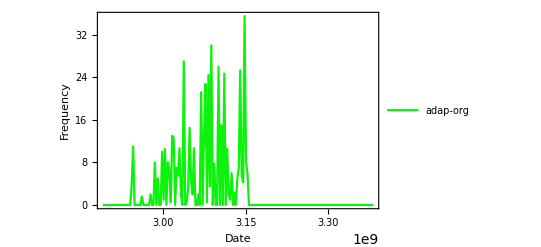

```mathematica
mFPlot[1]=mFPlot[1]
```

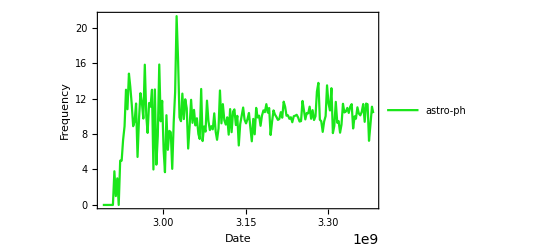

```mathematica
mFPlot[2]=mFPlot[2]
```

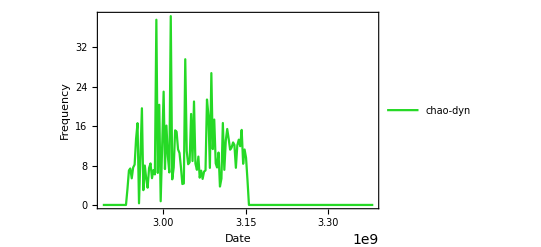

```mathematica
mFPlot[3]=mFPlot[3]
```

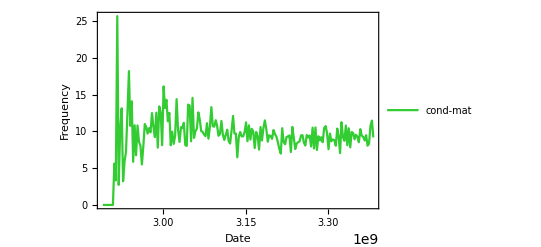

```mathematica
mFPlot[4]=mFPlot[4]
```

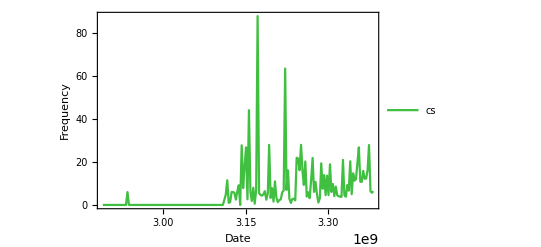

```mathematica
mFPlot[5]=mFPlot[5]
```

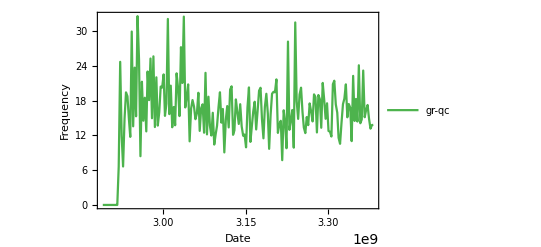

```mathematica
mFPlot[6]=mFPlot[6]
```

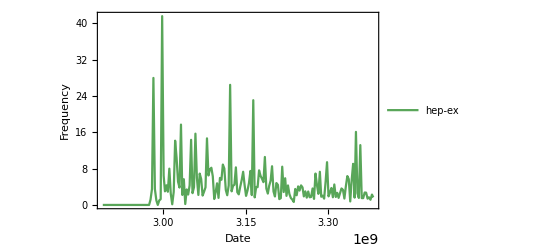

```mathematica
mFPlot[7]=mFPlot[7]
```

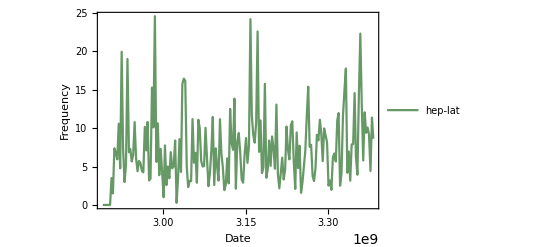

```mathematica
mFPlot[8]=mFPlot[8]
```

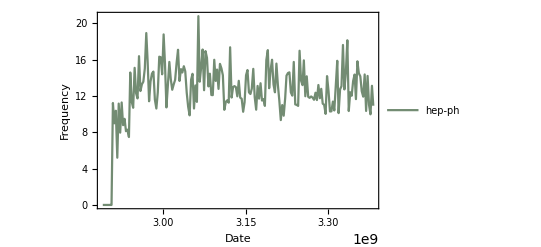

```mathematica
mFPlot[9]=mFPlot[9]
```

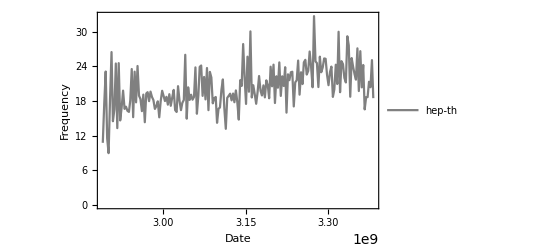

```mathematica
mFPlot[10]=mFPlot[10]
```

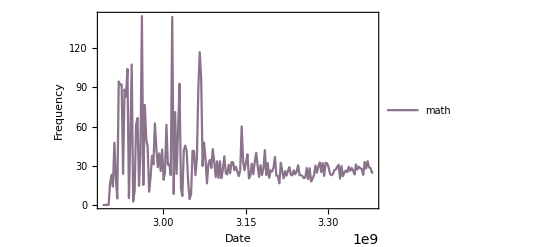

```mathematica
mFPlot[11]=mFPlot[11]
```

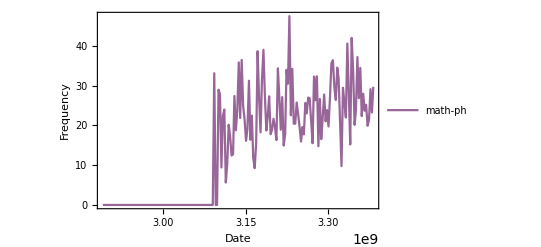

```mathematica
mFPlot[12]=mFPlot[12]
```

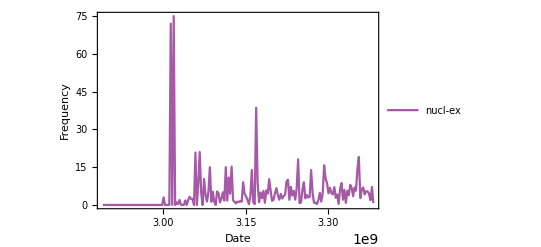

```mathematica
mFPlot[13]=meanFreqPlot[DateObject[{1991,08}],DateObject[{2007,3}],arXivNamesList[[13]],"α"]
```

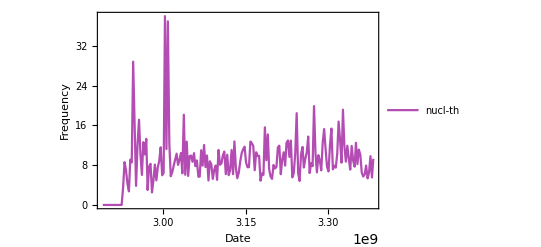

```mathematica
mFPlot[14]=mFPlot[14]
```

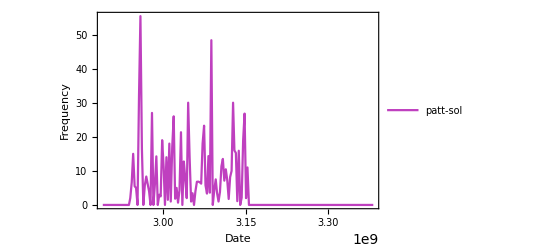

```mathematica
mFPlot[15]=mFPlot[15]
```

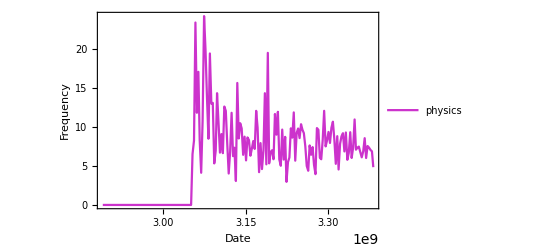

```mathematica
mFPlot[16]=mFPlot[16]
```

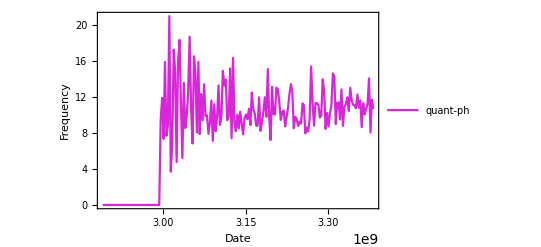

```mathematica
mFPlot[17]=mFPlot[17]
```

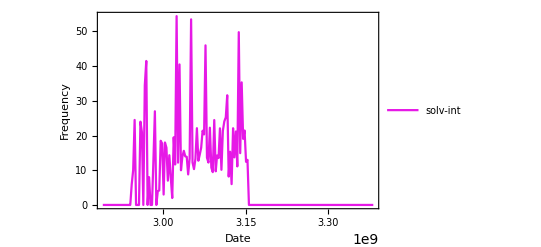

```mathematica
mFPlot[18]=mFPlot[18]
```

### More plots

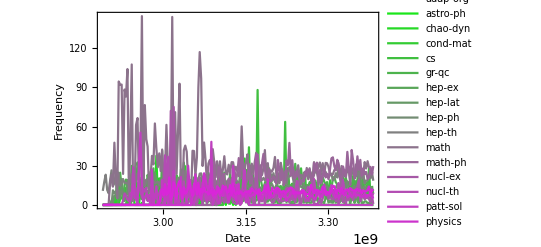

```mathematica
S =Show[Table[mFPlot[n],{n,17}], PlotRange->All]
```